## What is the Data Repository

https://datarepository.wolframcloud.com/

Recently released product that goes beyond the other repositories that have come out in the past few decades

Centralized repository that allows one to access user submitted data and WRI curated data

Provides convenient access to data beyond what is provided in the curated datasets from within Mathematica and the Wolfram Language

### What use is the Data Repository

Data loses much of its use if not provided in a computable format

By doing a little up-front curation data can be made useful to a broader audience

Having computable data means different datasets can easily be compared and connect

```mathematica
resources=RandomSample[ResourceSearch["Text",5],2]
```

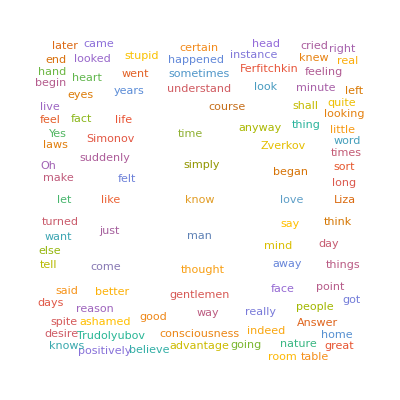
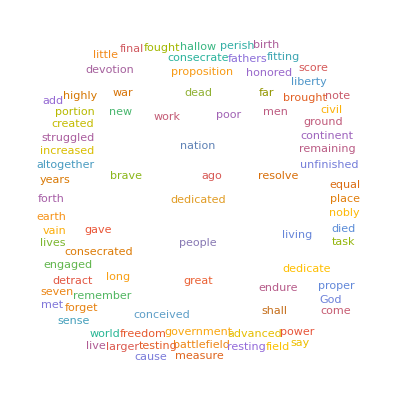

```mathematica
WordCloud@*
ResourceData/@{ResourceObject[…],ResourceObject[…]}
```

## Getting data from the Data Repository

On the web:

Open in Wolfram Cloud

Scroll to the bottom to the Data Downloads

Within the Wolfram Language

```mathematica
ResourceSearch["Entity Store of Books in Stephen Wolfram's Library"]
```

{ResourceObject[…]}

## Getting data from the Data Repository

```mathematica
ResourceObject[…]["Properties"]
```

{RepositoryLocation,Name,UUID,ResourceType,ContentSize,ContentElements,Version,Description,ContentTypes,Categories,Keywords,Attributes,LatestUpdate,DefaultReturnFormat,ContentElementAccessType,ContributorInformation,DefaultContentElement,Details,DOI,InformationElements,SeeAlso,ShortName,SourceMetadata,WolframLanguageVersionRequired,ResourceLocations,DownloadedVersion,Properties,DocumentationLink,ExampleNotebook}

```mathematica
ResourceData[ResourceObject[…]
]
```

EntityStore[<>]

```mathematica
PrependTo[$EntityStores,ResourceData[ResourceObject[…]
]]
```

{EntityStore[<>]}

```mathematica
EntityClass["SWLibraryBook","OLID"->Missing["NotAvailable"]]//EntityList//Length
```

589

## Submitting data to the Data Repository

Stephen laid out a curation hierarchy for preparing data for the data repository:

## Preparing Data for Submission

I pulled from JPL: https://spec.jpl.nasa.gov/ftp/pub/catalog/catdir.html

Loaded into CSV:

```mathematica
$raw=
With[{d=Import[FileNameJoin@{NotebookDirectory[],"JPL_Lines.csv"}]},
AssociationThread[First@d,#]&/@Rest[d]
];
```

## Preparing Data for Submission

```mathematica
Take[$raw,10]//Dataset
```

Dataset[<>]

```mathematica
$data=
Take[
GroupBy[
Association@*
KeyValueMap[
#->
Switch[#,
"Frequency",
Quantity[#2,"Megahertz"],
"LowerStateEnergy",
Quantity[#2,"Megahertz"],
"Transition",
With[{t=ToExpression[#2]},
Rule@@
Partition[t,
Length[t]/2//Floor
]
],
_,
#2
]&
]/@$raw,
Key["Tag"]
],
25
];
```

```mathematica
$data//Dataset
```

Dataset[<>]

## Preparing Data for Submission

Here’s a quick “derived property”

```mathematica
plotf=
ListPlot[
{QuantityMagnitude@#Frequency,#Weight}&/@
If[ListQ@#,#,{#}],
Filling->Axis,
PlotMarkers->"",
##2,
PlotStyle->Black
]&;
```

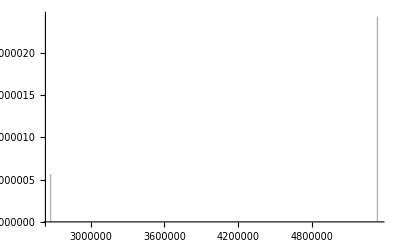

```mathematica
plotf@RandomChoice[$data]
```

## Creating a New ResourceObject

Create a new resource template notebook

Go to File » New » Other » Data Resource

Or programmatically:

```mathematica
CreateNotebook["DataResource"]
```

nkz96_shm22FrontEndObject[LinkObject["nkz96_shm", 3, 1]]22Untitled-3

Add basic info

## Creating a New ResourceObject

Add your content data:

```mathematica
CloudConnect["markb@wolfram.com"];
```

```mathematica
CloudExport[$data,"MX","jpl_lines.mx",Permissions->"Public"]
```

CloudObject[]

## Creating a New ResourceObject

Add examples:

Examples should be minimal, yet convey what is possible with the data

For examples of examples see the resources in the data repository already

## Submitting Data

If you are submitting to the public Data Repository you will now need to collect your metadata:

## Submitting Data

Specify any existing resources related to the resource you are submitting and select the relevant categories for your submission:

## Submitting Data

Specify any search keywords and, if you know it, provide the Dublin Core Metadata for your resource:

## Submitting Data

Finally, create your resource object:

Now one can deploy locally or to ones cloud account:

## Submitting Data

Deploying to ones own cloud account will render a shingle like those in the public repository:

## Submitting Data

To submit to the cloud one needs a Publisher ID. This can be gotten through the Data Repository website:

https://datarepository.wolframcloud.com/request-publisher-id

Submission will place your resource object into the standard review queue. Upon approval or rejection you will receive an email informing you of the status of your submission and -- if it was rejected -- what you can change so it will be approved:

## Demonstrations

http://demonstrations.wolfram.com

The Wolfram Demonstrations Project is an older project that aims to provide demonstrations for interesting phenomena and ideas, all using the Wolfram Language.

If you have a version of the CDF Player installed (and an appropriate web browser) you can view these demonstrations online. Otherwise you can download the CDF itself:

http://demonstrations.wolfram.com/LissajousPatternsOnASphereSurface/

## Creating Demonstrations

We can easily make our own demonstrations. First we open the template notebook

Go to File » New » Other » Demonstration

Or via WL

```mathematica
CreateNotebook["Demonstration"]
```

nkz96_shm33FrontEndObject[LinkObject["nkz96_shm", 3, 1]]33Untitled-5

We can also see how a demonstration was made by downloading the authoring notebook

## Challenges

Challenges is a new Wolfram project to provide coding challenges in the Wolfram Language

http://challenges.wolfram.com/

You can run challenges in the desktop or in the cloud

-Graphics-

## Creating a Challenge

We can also create our own challenges and submit them for review

Go to File » New » Other » Wolfram Challenge

## Creating a Challenge

We’ll first set up our basic challenge descriptions and a sample image:

## Creating a Challenge

Specify what the code should do and provide a quick example

## Creating a Challenge

Supply the input and solution

## Creating a Challenge

Finally, supply your test cases and authorship information and press Preview

## Creating a Challenge

Then preview before submitting:

This will generate a sample notebook, as it will be seen in the cloud